```mathematica
SetDirectory[NotebookDirectory[]];ClearAll["Global`*"];
Get["../sources/TriangleTools.m"]
ParallelEvaluate[$MinPrecision=2 $MachinePrecision];
```

```mathematica
PA={10+1/3,7.8881063774661547234231043887488227312206683077257870971729595588570966121408707156876700362441455708}; 
PB={0,0}; PC={6,0};
```

```mathematica
XX={1,0,0}; YY={0,1,0}; ZZ={0,0,1};
```

```mathematica
checkAubertLines[name_]:=Module[{A1, B1, C1, BE, i, AE, k, CE, l, PX, PY, PZ, det, XU},
Clear[a,b,c];Get["../sources/TriangleExpressions.m"]; Get["../sources/KimberlingTriangles.m"];
A1=KimberlingTrianglesTrilinear[name];
B1=Permute[A1,Cycles[{{2,3,1}}]]/.{a->b,b->c, c->a};
C1=Permute[B1,Cycles[{{2,3,1}}]]/.{a->b,b->c, c->a};
a=6; b=9; c=13;
{A1,B1,C1}=bFromTrilinear/@{N[A1,30],N[B1,30], N[C1,30]};
BE = bIntersection[A1,B1,C1, YY];
(*Aubertline(A',B',C',B)*)
i=bLine[bCoordChange[orth[A1, YY, BE],A1, YY, BE],bCoordChange[orth[B1, C1, BE],B1, C1, BE]];
AE = bIntersection[C1,A1,B1, XX];
(*Aubertline(C',A',B',A)*)
k=bLine[bCoordChange[orth[C1, XX, AE],C1, XX, AE],bCoordChange[orth[A1,B1, AE], A1,B1, AE]];
CE = bIntersection[A1,C1,B1, ZZ];
(*Aubertline(A',C',B',C)*)
l=bLine[bCoordChange[orth[A1, ZZ, CE],A1, ZZ, CE],bCoordChange[orth[C1,B1, CE], C1,B1, CE]];
PX=bLineIntersection[i,l]; 
PY=bLineIntersection[k,l]; 
PZ=bLineIntersection[i,k];
det = Det[{bLine[A1,PX],bLine[B1,PY],bLine[C1,PZ]}]//N;
XU = bLineIntersection[bLine[A1,PX],bLine[B1,PY]];
(* return te concurrency check, the cartesian and the baricyentrics *)
{det, N[Dot[XU/Total[XU],{PA,PB,PC}],20] , N[XU/Total[XU],20]}
]
```

```mathematica
Get["../sources/KimberlingTriangles.m"];cnt=1;
Do[
If[cnt>0,
cnt=cnt+1; Print[x];check = checkAubertLines[x];
If[
Abs[check[[1]]]<10^-10 && !(check[[2]][[1]]===Indeterminate),
Print[check[[2]]];Print[check[[3]]];
]
]; cnt=cnt+1;,
{x,{"Lucas reflection","Lucas(-1) reflection","Lucas secondary central","Lucas(-1) secondary central","Lucas 1st secondary tangents","Lucas(-1) 1st secondary tangents","Lucas 2nd secondary tangents","Lucas(-1) 2nd secondary tangents","Lucas tangents","Lucas(-1) tangents","1st Savin","2nd Savin","2nd inner-Soddy","2nd outer-Soddy","1st tri-square","2nd tri-square","3rd tri-square","4th tri-square","1st tri-square-central","2nd tri-square-central","3rd tri-square-central","4th tri-square-central","2nd inner-Vecten","3rd inner-Vecten","2nd outer-Vecten triangle","3rd outer-Vecten","Vu-Dao-X(15)-isodynamic equilateral","Vu-Dao-X(16)-isodynamic equilateral"}}
]
```

Lucas reflection

Lucas(-1) reflection

Lucas secondary central

Lucas(-1) secondary central

Lucas 1st secondary tangents

Lucas(-1) 1st secondary tangents

Lucas 2nd secondary tangents

Lucas(-1) 2nd secondary tangents

Lucas tangents

{7.2993054631339821872,0.41751216835077549302}

{0.052929327822387991212,-0.17832417376171681532,1.1253948459393288241}

Lucas(-1) tangents

{-117.70751290538395,15.826557989251577}

{2.006382423348535,22.066972789982378,-23.073355213330913}

1st Savin

2nd Savin

2nd inner-Soddy

{5.1465879754129600757,1.4055420524916255165}

{0.17818497687947239355,0.2709244873996811605,0.55089053572084644596}

2nd outer-Soddy

{6.252903733009859565,0.065106215504991337286}

{0.0082537192564972716352,-0.036189602705284120214,1.0279358834487868486}

1st tri-square

2nd tri-square

3rd tri-square

4th tri-square

1st tri-square-central

2nd tri-square-central

3rd tri-square-central

4th tri-square-central

2nd inner-Vecten

{-1.096324275520384209,2.3334908908470923188}

{0.29582396321544848013,1.396371352686776826,-0.69219531590222530618}

3rd inner-Vecten

2nd outer-Vecten triangle

{5.532713810276472918,0.73151333740581069332}

{0.092736241424876673713,0.14485720598299877802,0.76240655259212454827}

3rd outer-Vecten

Vu-Dao-X(15)-isodynamic equilateral

Vu-Dao-X(16)-isodynamic equilateral

```mathematica
(*checkAubertLines["K798i"]*)
```

```mathematica
Keys[KimberlingTrianglesTrilinear]
```

```mathematica
Clear[a,b,c];Get["../sources/TriangleExpressions.m"]; Get["../sources/KimberlingTriangles.m"];
A1=KimberlingTrianglesTrilinear["8th Fermat-Dao equilateral triangle"]
B1=Permute[A1,Cycles[{{2,3,1}}]]/.{a->b,b->c, c->a}
C1=Permute[B1,Cycles[{{2,3,1}}]]/.{a->b,b->c, c->a}
```

{(2 (-√((a+b-c) (a-b+c) (-a+b+c) (a+b+c))+√3 (1/2 (a^2+b^2-c^2)+1/2 (a^2-b^2+c^2))))/(a (-1/2 √((a+b-c) (a-b+c) (-a+b+c) (a+b+c))+1/2 √3 (-a^2+b^2+c^2))),1/b,1/c}

{1/a,(2 (-√((a+b-c) (a-b+c) (-a+b+c) (a+b+c))+√3 (1/2 (a^2+b^2-c^2)+1/2 (-a^2+b^2+c^2))))/(b (-1/2 √((a+b-c) (a-b+c) (-a+b+c) (a+b+c))+1/2 √3 (a^2-b^2+c^2))),1/c}

{1/a,1/b,(2 (-√((a+b-c) (a-b+c) (-a+b+c) (a+b+c))+√3 (1/2 (a^2-b^2+c^2)+1/2 (-a^2+b^2+c^2))))/(c (-1/2 √((a+b-c) (a-b+c) (-a+b+c) (a+b+c))+1/2 √3 (a^2+b^2-c^2)))}

```mathematica
a=6; b=9; c=13;
{A1,B1,C1}=bFromTrilinear/@{N[A1,20],N[B1,20], N[C1,20]};

(*A1={u,v,1-u-v}/.{u->1/3,v->-0.04831375729529248106574546679086364192};*)

BE = bIntersection[A1,B1,C1, YY];
(*Aubertline(A',B',C',B)*)
i=bLine[bCoordChange[orth[A1, YY, BE],A1, YY, BE],bCoordChange[orth[B1, C1, BE],B1, C1, BE]];

AE = bIntersection[C1,A1,B1, XX];
(*Aubertline(C',A',B',A)*)
k=bLine[bCoordChange[orth[C1, XX, AE],C1, XX, AE],bCoordChange[orth[A1,B1, AE], A1,B1, AE]];

CE = bIntersection[A1,C1,B1, ZZ];
(*Aubertline(A',C',B',C)*)
l=bLine[bCoordChange[orth[A1, ZZ, CE],A1, ZZ, CE],bCoordChange[orth[C1,B1, CE], C1,B1, CE]];
PX=bLineIntersection[i,l]; 
PY=bLineIntersection[k,l]; 
PZ=bLineIntersection[i,k];
Det[{bLine[A1,PX],bLine[B1,PY],bLine[C1,PZ]}]//N
```

0.0833128

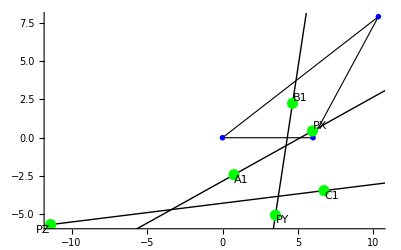

```mathematica
pts={PA, PB, PC}; 
pts2 = bToCartesian/@{PX, PY, PZ, A1, B1, C1};
names2 = {"PX","PY","PZ", "A1", "B1", "C1"};
Graphics[{Join[
{EdgeForm[{Thin, Black}], FaceForm[], Polygon [pts]},\
{pts/.{x_,y_}:>{Blue,PointSize[0.01],Point[{x,y}]}}, \
{pts2/.{x_,y_}:>{Green,PointSize[0.02],Point[{x,y}]}},
Text[#[[1]],#[[2]],-1.5 Sign@#[[2]]]&/@Transpose@{names2,pts2}],
{InfiniteLine[bToCartesian/@{A1,PX}], InfiniteLine[bToCartesian/@{B1,PY}], InfiniteLine[bToCartesian/@{C1,PZ}]}},
Axes->True, AspectRatio->Automatic
]
```

```mathematica
(*pts={PA, PB, PC}; 
pts2 = bToCartesian/@{PX, PY, PZ};
names2 = {"PX","PY","PZ"};
pts3 = bToCartesian/@{A1, B1, C1};
names3 = {"A1", "B1", "C1"};
icart = InfiniteLine[bToCartesian/@{bCoordChange[orth[A1, YY, BE],A1, YY, BE],bCoordChange[orth[B1, C1, BE],B1, C1, BE]}];
kcart = InfiniteLine[bToCartesian/@{bCoordChange[orth[C1, XX, AE],C1, XX, AE],bCoordChange[orth[A1,B1, AE], A1,B1, AE]}];
lcart=InfiniteLine[bToCartesian/@{bCoordChange[orth[A1, ZZ, CE],A1, ZZ, CE],bCoordChange[orth[C1,B1, CE], C1,B1, CE]}];
Graphics[{
Join[
{EdgeForm[{Thin, Black}], FaceForm[], Polygon [pts]},\
{pts/.{x_,y_}:>{Blue,PointSize[0.01],Point[{x,y}]}}, \
{pts3/.{x_,y_}:>{Green,PointSize[0.02],Point[{x,y}]}},
Text[#[[1]],#[[2]],-1.5 Sign@#[[2]]]&/@Transpose@{names3,pts3}],
{icart, kcart, lcart}, PlotRange->{{-10,10},{-10,10}}
}
]*)
```

```mathematica
N/@{A1/Total[A1],B1/Total[B1],C1/Total[C1]}
```

{{-0.305622,0.652811,0.652811},{0.284106,0.431788,0.284106},{-0.436917,-0.436917,1.87383}}

```mathematica
bDistance[A1,B1]-bDistance[A1,C1]
```

0.